The effect of disease types and gender on heart rate

The datafile contains heart rate data for various disease classes for a little less than 1000 patients. 5 disease superclasses (NORM, HYP, STTC, MI and CD) and sex (m,F)  are provided.

Factors to be analysed:
In a one way ANOVA: Factor A (Disease)
In a two way ANOVA:  Factor A( Disease) and	Factor B (Sex)
Outcome variable was the heart rate of the individuals.

Load the data, split it into groups, and display descriptive statistics

Read the data file  beer_goggles_effect.xls, modifying the path below as necessary.
This contains columns containing the gender of the participant, amount of alcohol they drunk, and the (independently-rated) attractiveness of the person they selected.
Flatten is used to remove any unnecessary levels of nested lists.

```mathematica
dataset = SetDirectory["D:\\University_of_Aberdeen\\Semester_2\\PX5510_Statistics_and_Time_Series_Analysis\\Time Series Analysis\\Practicals\\Dataset"]
```

D:\University_of_Aberdeen\Semester_2\PX5510_Statistics_and_Time_Series_Analysis\Time Series Analysis\Practicals\Dataset

```mathematica
data=Import[FileNameJoin[{dataset,"HeartRate_DiseaseClass_sex_1000.csv"}]];
```

```mathematica
data//TableView
```

sexdiagnostic_superclassHeartRate(bmp)FSTTC78.9473684210525FSTTC84.5070422535211MSTTC96.7741935483871FSTTC74.0740740740741FSTTC71.4285714285714MSTTC93.7499999999999MSTTC59.4059405940594FSTTC62.5FSTTC71.4285714285714FSTTC80.FSTTC68.1818181818182FSTTC98.3606557377049FSTTC67.0391061452514FSTTC68.1818181818182MSTTC78.9473684210526FSTTC86.3309352517986MSTTC95.2380952380952MSTTC54.5454545454545FSTTC46.1538461538462FSTTC76.9230769230769FSTTC54.7945205479452FSTTC92.3076923076923FSTTC77.9220779220779FSTTC96.7741935483871MSTTC71.0059171597633MSTTC52.6315789473684FSTTC102.564102564103FSTTC86.9565217391304FSTTC69.7674418604652MSTTC93.75FSTTC85.7142857142857MSTTC67.4157303370787FSTTC78.9473684210526FSTTC57.6923076923077FSTTC55.2995391705069MSTTC76.9230769230769FSTTC61.2244897959184MSTTC52.863436123348FSTTC75.9493670886076MSTTC37.037037037037FSTTC77.4193548387097FSTTC53.8116591928251MSTTC56.8720379146919FSTTC88.8888888888889FSTTC60.FSTTC45.8015267175573FSTTC67.4157303370787MSTTC101.694915254237FSTTC100.FSTTC81.0810810810811MSTTC68.9655172413793MSTTC64.516129032258FSTTC35.2941176470588FSTTC86.3309352517986FSTTC79.4701986754967MSTTC56.6037735849057MSTTC68.9655172413793FSTTC54.5454545454545FSTTC63.1578947368421FSTTC59.4059405940594FSTTC66.2983425414365FSTTC65.2173913043478FSTTC83.3333333333333FSTTC81.6326530612245MSTTC36.9230769230769FSTTC67.7966101694915FSTTC91.6030534351145FSTTC84.5070422535211FSTTC57.9710144927536MSTTC103.448275862069MSTTC82.1917808219178MSTTC11.5163147792706FSTTC101.694915254237FSTTC58.252427184466MSTTC68.9655172413793FSTTC72.289156626506MSTTC101.694915254237FSTTC49.5867768595041FSTTC130.434782608695FSTTC121.212121212121FSTTC64.5161290322581MSTTC83.3333333333333FSTTC75.9493670886076FSTTC95.2380952380952FSTTC59.1133004926108FSTTC78.4313725490196FSTTC75.9493670886076MSTTC95.2380952380952FSTTC82.1917808219178FSTTC69.7674418604651FSTTC82.1917808219178FSTTC82.1917808219178FSTTC89.5522388059701FSTTC129.032258064516FSTTC78.9473684210526FSTTC70.5882352941177FSTTC63.8297872340426FSTTC82.1917808219178MSTTC71.4285714285714MSTTC58.252427184466FSTTC85.7142857142857MSTTC82.1917808219178FSTTC67.4157303370787FSTTC66.6666666666667MSTTC73.1707317073172FSTTC104.347826086957FSTTC92.3076923076923FSTTC38.2165605095541FSTTC12.1703853955375FSTTC44.7761194029851FSTTC80.FSTTC78.9473684210525FSTTC44.1176470588235MSTTC70.1754385964912MSTTC96.7741935483871MSTTC83.3333333333333MSTTC65.2173913043478MSTTC57.1428571428571MSTTC113.207547169811MSTTC69.364161849711MSTTC92.3076923076923MSTTC70.1754385964912MSTTC72.289156626506FSTTC66.2983425414365FSTTC90.9090909090909MSTTC82.1917808219178FSTTC56.6037735849057FSTTC111.111111111111MSTTC55.045871559633FSTTC86.9565217391304FSTTC60.FSTTC95.2380952380951FNORM64.1711229946524MNORM46.1538461538462FNORM63.8297872340426MNORM75.9493670886076FNORM66.6666666666667FNORM82.1917808219178MNORM61.8556701030928MNORM60.6060606060606FNORM62.5FNORM68.5714285714286FNORM48.FNORM77.9220779220779FNORM75.9493670886076FNORM58.8235294117647MNORM81.0810810810813MNORM57.6923076923077FNORM73.1707317073171MNORM54.5454545454545FNORM88.2352941176471MNORM63.8297872340426FNORM95.2380952380952FNORM67.7966101694915FNORM75.MNORM74.0740740740741MNORM90.2255639097744FNORM57.1428571428571MNORM72.289156626506MNORM64.5161290322581FNORM57.6923076923077FNORM78.9473684210526MNORM82.7586206896552MNORM76.4331210191083FNORM64.5161290322581FNORM73.1707317073172FNORM71.8562874251497FNORM88.2352941176471MNORM64.8648648648649FNORM77.4193548387097MNORM71.0059171597633MNORM54.5454545454545MNORM69.364161849711FNORM71.4285714285714FNORM67.0391061452514FNORM63.1578947368422FNORM77.4193548387097FNORM44.4444444444444FNORM73.1707317073171MNORM69.7674418604652FNORM59.4059405940594MNORM59.7014925373134FNORM65.2173913043478MNORM51.5021459227468FNORM61.2244897959184MNORM44.280442804428MNORM59.4059405940594MNORM93.0232558139535FNORM64.5161290322581FNORM60.FNORM68.9655172413793FNORM92.3076923076923MNORM62.4999999999999FNORM76.9230769230769MNORM67.4157303370787MNORM54.5454545454545MNORM69.7674418604652FNORM71.4285714285714FNORM58.252427184466MNORM70.5882352941177MNORM83.9160839160839MNORM58.8235294117647MNORM60.9137055837564MNORM64.5161290322581MNORM68.9655172413793FNORM58.8235294117647FNORM95.2380952380952FNORM65.2173913043478MNORM82.1917808219178FNORM78.9473684210526FNORM120.FNORM69.7674418604652FNORM65.9340659340659MNORM65.2173913043478MNORM70.1754385964912FNORM96.7741935483871FNORM64.5161290322581FNORM71.4285714285713FNORM59.4059405940594FNORM60.6060606060606MNORM61.2244897959184FNORM82.7586206896552MNORM62.1761658031088FNORM58.252427184466FNORM66.2983425414365MNORM62.5FNORM67.4157303370787MNORM67.0391061452514FNORM55.5555555555556FNORM70.5882352941176FNORM74.9999999999999FNORM59.4059405940594MNORM65.9340659340659FNORM72.289156626506FNORM73.1707317073171FNORM78.9473684210526FNORM82.1917808219178MNORM84.5070422535211FNORM56.6037735849057MNORM63.1578947368422FNORM67.4157303370787FNORM72.2891566265059FNORM93.0232558139535MNORM65.2173913043478MNORM55.5555555555556MNORM74.0740740740741FNORM63.4920634920635FNORM53.3333333333333FNORM56.8720379146919FNORM63.1578947368422MNORM61.2244897959184MNORM61.2244897959184MNORM92.3076923076923MNORM64.5161290322581FNORM65.5737704918033MNORM73.1707317073171FNORM60.6060606060606FNORM62.5FNORM84.5070422535211MNORM49.1803278688525MNORM81.0810810810811FNORM64.5161290322581FNORM66.2983425414365FNORM80.FNORM67.4157303370787FNORM75.9493670886075MNORM50.8474576271186FNORM96.7741935483871FNORM76.4331210191083MNORM64.1711229946524MNORM96.7741935483871FNORM89.5522388059701FNORM69.7674418604651MNORM75.MNORM76.9230769230768FNORM53.8116591928251FNORM61.2244897959184FNORM56.0747663551402FNORM74.0740740740741MNORM65.2173913043478MNORM63.8297872340426FNORM88.2352941176471FNORM72.289156626506FNORM95.2380952380952MNORM61.2244897959184FNORM65.9340659340659MNORM51.2820512820513FNORM48.7804878048781MNORM100.FNORM55.2995391705069MNORM74.074074074074FNORM68.9655172413793FNORM77.9220779220779MNORM75.MNORM58.8235294117647FNORM80.MNORM72.289156626506MNORM63.4920634920635FNORM75.4716981132075FNORM68.1818181818182MNORM58.5365853658537MNORM64.8648648648649FNORM55.8139534883721MNORM73.1707317073171MNORM63.157894736842MNORM65.9340659340659FNORM76.923076923077FNORM58.8235294117647MNORM64.1711229946524FNORM88.2352941176471MNORM68.9655172413793MNORM63.4920634920635FNORM73.1707317073171FNORM66.6666666666667FNORM77.9220779220779FNORM96.7741935483871MNORM56.0747663551402FNORM81.0810810810811MNORM66.6666666666667MNORM63.8297872340426MNORM80.MNORM88.2352941176471MNORM53.8116591928251MNORM54.5454545454545MNORM57.6923076923077FNORM84.5070422535211MNORM81.0810810810811MNORM64.8648648648649FNORM73.1707317073171MNORM62.4999999999999MNORM50.4201680672269MNORM65.5737704918033FNORM69.7674418604651FNORM66.2983425414365FNORM57.6923076923077FNORM68.5714285714286MNORM63.1578947368421FNORM68.9655172413792MNORM73.1707317073171FNORM98.3606557377049FNORM70.5882352941177FNORM65.2173913043478FNORM54.0540540540541FNORM75.9493670886076FNORM61.2244897959184FNORM65.9340659340659FNORM83.3333333333333MNORM78.4313725490196FNORM58.252427184466MNORM68.9655172413793FNORM79.4701986754967FNORM55.5555555555556MNORM66.2983425414365MNORM57.4162679425837MNORM51.063829787234FNORM67.4157303370787FNORM55.5555555555556MNORM51.948051948052FNORM62.1761658031088FNORM68.9655172413793FNORM83.3333333333332FNORM75.4716981132075FNORM76.4331210191083MNORM67.4157303370787MNORM65.5737704918033MNORM67.4157303370787FNORM68.5714285714286MNORM65.2173913043478FNORM74.0740740740741FNORM81.6326530612245FNORM86.9565217391304FNORM71.4285714285714MNORM69.7674418604651MNORM50.2092050209205MNORM67.7966101694915MNORM56.6037735849057MNORM65.9340659340659FNORM79.4701986754967MNORM63.4920634920635MNORM15.0943396226415FNORM68.9655172413793MNORM55.045871559633FNORM67.0391061452514MNORM84.5070422535211MNORM65.9340659340659MNORM82.1917808219178FNORM81.0810810810811FNORM65.5737704918033MNORM89.5522388059701FNORM68.1818181818181FNORM81.0810810810811FNORM70.5882352941176MNORM68.9655172413793FNORM69.364161849711MNORM73.1707317073172MNORM66.6666666666667FNORM68.9655172413792MNORM74.9999999999999MNORM65.9340659340659FNORM47.0588235294118MNORM94.488188976378MNORM78.9473684210526MNORM57.6923076923077FNORM80.FNORM81.0810810810811FNORM64.5161290322581FNORM64.5161290322581MNORM48.3870967741936MNORM54.7945205479452MNORM70.5882352941177FNORM51.7241379310345FNORM74.0740740740741MNORM84.507042253521FNORM60.6060606060606FNORM64.5161290322581MNORM80.5369127516778MNORM66.6666666666667FNORM72.289156626506FNORM75.4716981132075FNORM54.2986425339367MNORM74.0740740740741FNORM75.FNORM66.2983425414365MNORM57.1428571428571FNORM67.0391061452514MNORM91.6030534351145MNORM63.157894736842MNORM31.0880829015544MNORM41.0958904109589MNORM77.9220779220779FNORM71.4285714285714FNORM74.0740740740741MNORM73.1707317073171MNORM80.FNORM93.0232558139535MNORM31.9148936170213FNORM73.1707317073171FNORM73.1707317073171MNORM61.8556701030927MNORM62.8272251308901MNORM74.074074074074FNORM83.3333333333333FNORM83.3333333333332FNORM80.5369127516778FNORM99.1735537190083MNORM63.8297872340426MNORM67.4157303370786FNORM85.7142857142858MNORM53.3333333333333MNORM61.8556701030928FNORM65.9340659340659FNORM75.9493670886076FNORM63.8297872340426MNORM76.4331210191083MNORM74.0740740740741FNORM67.4157303370787FNORM75.9493670886077FNORM78.9473684210526FNORM81.0810810810811FNORM76.9230769230769FNORM80.FNORM74.0740740740741MNORM66.6666666666667FNORM61.2244897959184FNORM76.9230769230769FNORM59.4059405940594FNORM59.4059405940594FNORM81.0810810810811FNORM73.1707317073171FNORM64.5161290322581MNORM68.1818181818182MNORM113.207547169811MNORM98.3606557377049MNORM60.6060606060606MNORM96.7741935483871FNORM53.3333333333333MNORM70.5882352941177MNORM64.5161290322581FNORM81.0810810810811FNORM65.9340659340659FNORM73.1707317073171FNORM64.8648648648649FNORM62.8272251308901MNORM84.5070422535211FNORM67.7966101694915FNORM69.7674418604651MNORM61.8556701030927MNORM61.2244897959184FNORM60.6060606060606FNORM60.MNORM52.1739130434783FNORM49.1803278688525FNORM68.1818181818182FNORM66.6666666666667FNORM74.074074074074FNORM73.1707317073172FNORM77.9220779220779FNORM53.5714285714286FNORM73.6196319018405MNORM54.5454545454545MNORM67.7966101694915FNORM67.4157303370787MNORM58.8235294117647FNORM89.5522388059701FNORM88.2352941176471FNORM74.0740740740741FNORM59.4059405940594FNORM80.MNORM53.3333333333333FNORM75.MNORM63.157894736842FNORM95.2380952380952MNORM82.1917808219178FNORM70.5882352941177FNORM74.074074074074FNORM57.9710144927536FNORM56.0747663551402MNORM67.4157303370787MNORM84.5070422535211FNORM77.4193548387097FNORM74.074074074074FNORM74.0740740740741MNORM75.9493670886076FNORM95.2380952380951FNORM70.5882352941176FNORM50.FNORM66.6666666666667FNORM53.5714285714286MNORM82.1917808219178FNORM77.9220779220779FNORM61.5384615384615MNORM60.3015075376884MNORM60.6060606060606MNORM72.7272727272727FNORM111.111111111111FNORM61.2244897959184MNORM91.6030534351145FNORM31.413612565445FNORM63.1578947368422FNORM93.7499999999999FNORM73.1707317073172MNORM54.2986425339367MNORM74.074074074074FNORM75.FNORM68.1818181818182MNORM88.8888888888889FNORM82.1917808219178FNORM83.3333333333333FNORM103.448275862069FNORM60.6060606060606FNORM64.1711229946524FNORM103.448275862069FNORM70.1754385964911FNORM69.7674418604652MNORM68.9655172413794MNORM78.9473684210525MNORM80.FNORM78.9473684210526FNORM77.9220779220779MNORM55.5555555555556FNORM89.5522388059703MNORM90.2255639097744FNORM66.6666666666667MNORM63.8297872340426MNORM65.9340659340659MNORM82.1917808219178FNORM75.9493670886076MNORM45.1127819548872MNORM60.6060606060606MNORM84.5070422535211MNORM64.1711229946524FNORM74.0740740740741MNORM75.FNORM80.FNORM68.1818181818182MNORM60.6060606060607FNORM68.5714285714286MNORM65.2173913043478MNORM63.4920634920635FNORM89.5522388059701MNORM55.045871559633FNORM93.75FNORM64.5161290322581MNORM81.081081081081FNORM78.9473684210526FNORM19.5758564437194MNORM67.4157303370787FNORM74.0740740740741FNORM75.9493670886076MNORM51.7241379310345FNORM61.2244897959184MNORM117.647058823529FNORM77.9220779220779MNORM77.9220779220779FNORM101.694915254237FNORM86.9565217391304FNORM86.3309352517986FNORM72.7272727272727FNORM77.9220779220779MNORM71.4285714285714MNORM76.4331210191083FNORM81.0810810810811FNORM117.647058823529MNORM55.2995391705069MNORM63.8297872340426MNORM64.8648648648649FNORM62.5FNORM86.9565217391304FNORM58.8235294117647MNORM83.3333333333333MNORM58.252427184466FNORM86.9565217391304FNORM72.289156626506MNORM96.7741935483871MNORM58.8235294117647MNORM57.4162679425837MNORM72.289156626506MNORM83.3333333333333MNORM72.289156626506FNORM52.1739130434783FNORM76.9230769230769MNORM74.5341614906832MNORM80.5369127516778FNORM55.2995391705069MNORM67.7966101694915MNORM56.0747663551402FNORM80.MNORM60.6060606060606FNORM86.9565217391304MNORM73.1707317073171MNORM71.0059171597633FNORM63.1578947368421FNORM75.9493670886076MNORM55.5555555555556FNORM85.7142857142857MNORM81.0810810810811MNORM67.0391061452514FNORM63.8297872340426MNORM63.8297872340426FNORM71.8562874251497FNORM52.1739130434783FNORM60.6060606060606FNORM75.MNORM54.2986425339367FNORM83.3333333333332FNORM71.4285714285714FNORM84.5070422535211FNORM58.252427184466MNORM81.0810810810811FNORM56.0747663551402FNORM69.7674418604652MNORM68.1818181818181FNORM68.1818181818182FNORM76.923076923077FNORM66.6666666666667FNORM29.3398533007335MNORM60.6060606060606MNORM67.4157303370787FNORM59.4059405940594FNORM65.5737704918033FNORM82.7586206896551FNORM76.9230769230769MNORM67.4157303370787MNORM82.1917808219178FNORM89.5522388059701MNORM68.5714285714287FNORM90.2255639097744MNORM64.5161290322581MNORM56.6037735849057FNORM71.4285714285714FNORM69.7674418604651FNORM64.516129032258FNORM57.4162679425837MNORM74.074074074074MNORM58.8235294117647FNORM87.5912408759124FNORM64.1711229946524FNORM104.347826086957FNORM68.9655172413793MNORM83.3333333333333MNORM61.5384615384615FNORM42.5531914893617FNORM55.8139534883721MNORM71.4285714285714FNORM59.4059405940594FNORM73.1707317073171MNORM70.5882352941177MNORM71.4285714285714MNORM62.4999999999999FNORM56.6037735849057MNORM65.9340659340659MNORM88.2352941176469MNORM68.1818181818182MNORM70.5882352941177FNORM70.1754385964912FNORM74.0740740740741MNORM71.4285714285714FNORM67.0391061452515FNORM77.4193548387097MNORM74.0740740740741FNORM90.9090909090909FNORM54.0540540540541MNORM78.9473684210526FNORM62.5FNORM63.8297872340426FNORM111.111111111111FNORM96.7741935483873FNORM74.074074074074FNORM61.8556701030928MNORM67.4157303370787FNORM75.4716981132075FNORM113.207547169812MMI74.074074074074FMI45.8015267175573MMI60.6060606060606MMI69.364161849711MMI105.263157894737MMI48.9795918367347FMI67.4157303370787MMI78.9473684210526MMI59.4059405940594MMI25.MMI55.5555555555556FMI96.7741935483871MMI75.MMI49.5867768595041FMI88.2352941176471FMI107.142857142857FMI68.1818181818182FMI66.6666666666667FMI79.4701986754967MMI100.840336134454MMI92.3076923076923FMI66.6666666666667FMI82.1917808219178MMI85.7142857142858MMI69.7674418604651FMI86.9565217391304FMI98.3606557377049MMI62.8272251308901MMI56.6037735849057MMI59.4059405940594MMI52.1739130434783FMI71.4285714285713MMI69.7674418604651MMI72.289156626506MMI90.9090909090909MMI60.6060606060606MMI75.9493670886076MMI59.4059405940594MMI90.9090909090909MMI55.2995391705069MMI82.1917808219178FMI76.4331210191083MMI68.9655172413793MMI110.091743119266FMI75.9493670886076FMI64.516129032258FMI136.363636363636FMI80.FMI82.1917808219179FMI42.2535211267606FMI63.4920634920635FMI120.FMI57.6923076923077FMI81.6326530612245FMI78.9473684210525FMI73.1707317073171FMI72.289156626506FMI72.289156626506FMI79.4701986754967MMI77.9220779220779MMI84.5070422535211FMI82.1917808219178FMI90.9090909090909FMI71.4285714285714MMI101.694915254237MMI66.6666666666667MMI81.0810810810811MMI77.9220779220779MMI95.2380952380952FMI63.8297872340426FMI88.2352941176471FMI79.4701986754967FMI58.8235294117647FMI92.3076923076923FMI81.0810810810811FMI65.2173913043478MMI76.4331210191083MMI56.6037735849057FMI68.9655172413793MMI92.3076923076923MMI61.8556701030928MMI35.8208955223881MMI74.0740740740741FMI68.9655172413792FMI71.4285714285713FMI74.0740740740741MMI88.2352941176471MMI63.4920634920635MMI75.9493670886076MMI67.4157303370787MMI92.3076923076923MMI66.2983425414365FMI133.333333333334FMI50.4201680672269MMI72.289156626506MMI78.4313725490196MMI77.9220779220779MMI54.0540540540541MMI96.7741935483871MMI67.0391061452514MMI89.5522388059701FMI19.1693290734824FMI76.9230769230769FMI72.7272727272727MMI65.9340659340659FMI68.9655172413793FMI76.9230769230769MMI65.9340659340659MMI17.2166427546628MMI77.9220779220779MMI68.1818181818182FMI109.090909090909FMI120.FMI49.1803278688525FMI88.8888888888889FMI40.2684563758389MMI77.9220779220779MMI59.4059405940594MMI67.0391061452514FMI112.14953271028MMI60.MMI63.1578947368421FMI65.2173913043478MMI57.6923076923077FMI88.2352941176471FMI56.6037735849057MMI82.1917808219178MMI103.448275862069FMI64.1711229946524FMI122.448979591837MMI75.9493670886076MMI81.6326530612245FMI111.111111111111FMI47.6190476190476FMI54.0540540540541FMI77.9220779220779FMI64.5161290322581FMI67.4157303370787MMI68.1818181818182MMI65.5737704918033MMI96.7741935483869MMI46.875MMI54.7945205479452FMI72.289156626506MMI63.1578947368421FMI56.6037735849057FMI52.6315789473684MMI50.4201680672269MMI82.1917808219178FMI46.875MMI53.0973451327434MMI89.55223880597MMI70.5882352941177MHYP63.8297872340426MHYP75.9493670886076FHYP49.5867768595041FHYP61.8556701030928FHYP72.289156626506FHYP59.7014925373134FHYP58.252427184466MHYP73.1707317073171MHYP150.MHYP90.9090909090909MHYP77.9220779220779FHYP77.9220779220779MHYP65.2173913043478MHYP51.5021459227468FHYP78.9473684210526MHYP98.3606557377049FHYP66.6666666666667MHYP74.074074074074FHYP57.6923076923077FHYP101.694915254237FHYP92.3076923076923MHYP71.4285714285714FHYP63.4920634920635MHYP56.6037735849057FHYP82.1917808219178FHYP81.0810810810811FHYP81.0810810810811MHYP62.1761658031088MHYP76.9230769230769FHYP68.1818181818182MHYP73.1707317073172FHYP78.4313725490196FHYP47.8087649402391MHYP88.2352941176471FHYP99.1735537190083MHYP65.2173913043478MHYP58.8235294117647MHYP81.0810810810811FHYP70.5882352941176FHYP108.108108108108MHYP65.5737704918033FHYP79.4701986754967FHYP67.4157303370787MHYP52.863436123348FHYP127.659574468085MHYP81.0810810810811MCD100.MCD72.7272727272727MCD92.3076923076923MCD86.9565217391304MCD77.4193548387097MCD71.4285714285714FCD61.8556701030928MCD82.1917808219178MCD68.1818181818182MCD76.9230769230769FCD44.280442804428FCD40.5405405405405MCD83.3333333333333FCD54.2986425339367FCD77.9220779220779FCD75.FCD95.2380952380952FCD80.FCD69.364161849711FCD96.7741935483871FCD73.1707317073171MCD54.2986425339367MCD68.5714285714286FCD81.0810810810811MCD72.289156626506FCD56.6037735849057MCD77.9220779220779MCD67.4157303370787FCD54.0540540540541FCD105.263157894737MCD71.4285714285713FCD75.9493670886075FCD69.364161849711MCD58.252427184466MCD69.7674418604651MCD70.5882352941176MCD62.5MCD48.MCD57.6923076923077FCD80.MCD85.7142857142858FCD53.0973451327434FCD75.9493670886075FCD69.7674418604652FCD48.MCD75.9493670886076FCD56.6037735849057FCD56.6037735849057MCD64.5161290322581MCD65.934065934066MCD93.7499999999999MCD58.8235294117647MCD78.9473684210526MCD80.MCD60.6060606060606MCD84.507042253521MCD100.MCD93.75MCD68.9655172413793FCD70.5882352941176MCD70.5882352941177FCD65.5737704918033MCD41.2371134020619FCD73.1707317073171FCD75.9493670886076MCD67.0391061452514MCD28.169014084507MCD54.5454545454545MCD62.4999999999999MCD75.9493670886076FCD68.5714285714286MCD67.4157303370787MCD56.8720379146919FCD68.9655172413793MCD63.1578947368421FCD68.5714285714286MCD66.2983425414365FCD76.9230769230768MCD150.FCD69.7674418604651FCD37.037037037037MCD84.5070422535211MCD70.5882352941177MCD92.3076923076923MCD68.5714285714286MCD41.2371134020619

Label of the first variable:

```mathematica
data[[1,1]]
```

sex

Number of data points including the labels:

```mathematica
Dimensions[data]
```

{998,3}

Number of data points excluding the labels:

```mathematica
Dimensions[data[[2;;,All]]]
```

{997,3}

Plot a box-whisker plot of all the heart rate data:

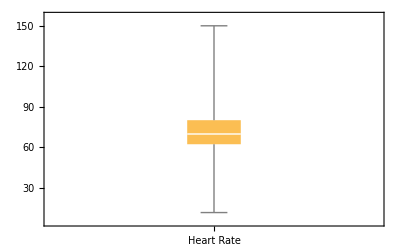

```mathematica
BoxWhiskerChart[data[[2;;,3]],ChartLabels->{"Heart Rate"}]
```

Display the mean, median, variance, and standard deviation of the heart rate data:

```mathematica
Through[{Mean,Median,Variance,StandardDeviation}[data[[2;;,3]]]]  //N
```

{71.6207,69.7674,256.848,16.0265}

```mathematica
Union[data[[2;;,2]]]
```

{CD,HYP,MI,NORM,STTC}

```mathematica
Tally[data[[2;;,2]]]
```

{{STTC,132},{NORM,580},{MI,153},{HYP,46},{CD,86}}

Lets initially divide into healthy and diseased

```mathematica
healthy=Select[data,#[[2]]=="NORM"&][[All,3]];
diseased=Select[data,#[[2]]!="NORM"&][[All,3]];
```

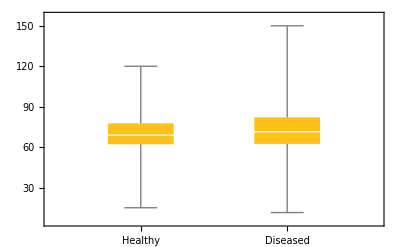

```mathematica
BoxWhiskerChart[{healthy,diseased},ChartLabels->{Healthy,Diseased}]
```

Split the heart rate data into the five categories for a one way ANOVA :
- All participants with no disease (NORM)
- All participants with CD
- All participants with STTC
- All participants with HYP
- All participants with MI

```mathematica
anorm=Select[data,#[[2]]=="NORM"&][[All,3]];
acd=Select[data,#[[2]]=="CD"&][[All,3]];
asttc=Select[data,#[[2]]=="STTC"&][[All,3]];
ahyp=Select[data,#[[2]]=="HYP"&][[All,3]];
ami=Select[data,#[[2]]=="MI"&][[All,3]];
```

We check the mean, std and variance for each category

```mathematica
Through[{Mean,StandardDeviation,Variance}[anorm]]
Through[{Mean,StandardDeviation,Variance}[acd]]
Through[{Mean,StandardDeviation,Variance}[asttc]]
Through[{Mean,StandardDeviation,Variance}[ahyp]]
Through[{Mean,StandardDeviation,Variance}[ami]]
```

{70.2638,13.1814,173.749}

{70.797,17.1441,293.92}

{74.3893,19.7417,389.734}

{75.7764,19.5746,383.165}

{73.5895,19.6035,384.298}

And the box whisker plots

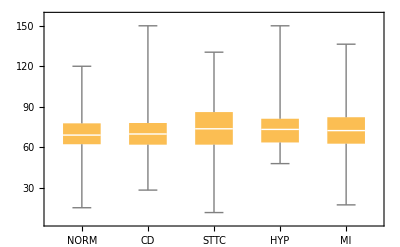

```mathematica
BoxWhiskerChart[{anorm,acd,asttc, ahyp, ami},ChartLabels->{"NORM", "CD","STTC", "HYP","MI"}]
```

```mathematica
<<ANOVA`
```

```mathematica
ANOVA[data[[2;;,{2,3}]]]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 3525.45 | 881.363 | 3.46544 | 0.0080326
Error | 992 | 252295. | 254.33 |  | 
Total | 996 | 255821. |  |  | ,CellMeans→All | 71.6207
Model[CD] | 70.797
Model[HYP] | 75.7764
Model[MI] | 73.5895
Model[NORM] | 70.2638
Model[STTC] | 74.3893}

The one way ANOVA shows that there is a significant difference between the means. We cannot find out between which classes yet. This would require multiple t-tests.
Lets move on to introduce another factor, the sex of the participants.

## Two way ANOVA

```mathematica
fem=Select[data,#[[1]]=="F"&][[All,3]];
mal=Select[data,#[[1]]=="M"&][[All,3]];
```

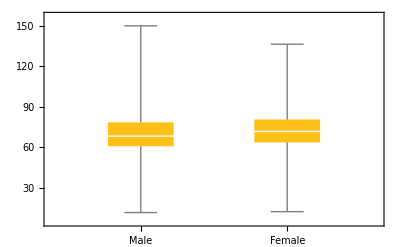

```mathematica
BoxWhiskerChart[{mal,fem},ChartLabels->{Male,Female}]
```

Now we split into ten groups: Male patients with each disease and female with each

```mathematica
mnorm=Select[data,And[#[[1]]=="M", #[[2]]=="NORM"]&][[All,3]];
mcd=Select[data,And[#[[1]]=="M", #[[2]]=="CD"]&][[All,3]];
msttc=Select[data,And[#[[1]]=="M", #[[2]]=="STTC"]&][[All,3]];
mhyp=Select[data,And[#[[1]]=="M", #[[2]]=="HYP"]&][[All,3]];
mmi=Select[data,And[#[[1]]=="M", #[[2]]=="MI"]&][[All,3]];
fnorm=Select[data,And[#[[1]]=="F", #[[2]]=="NORM"]&][[All,3]];
fcd=Select[data,And[#[[1]]=="F", #[[2]]=="CD"]&][[All,3]];
fsttc=Select[data,And[#[[1]]=="F", #[[2]]=="STTC"]&][[All,3]];
fhyp=Select[data,And[#[[1]]=="F", #[[2]]=="HYP"]&][[All,3]];
fmi=Select[data,And[#[[1]]=="F", #[[2]]=="MI"]&][[All,3]];
```

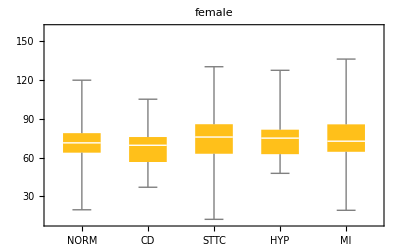
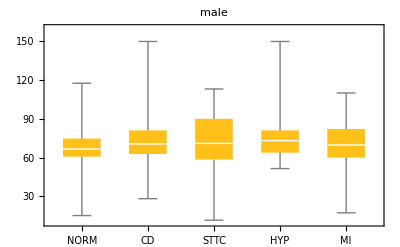

```mathematica
{BoxWhiskerChart[{fnorm,fcd,fsttc, fhyp, fmi},PlotRange->{10,160},
PlotLabel->female, ChartLabels->{"NORM", "CD","STTC", "HYP","MI"},ImageSize->{400,300}],BoxWhiskerChart[{mnorm,mcd,msttc, mhyp, mmi},PlotRange->{10,160},
PlotLabel->male, ChartLabels->{"NORM", "CD","STTC", "HYP","MI"},ImageSize->{400,300}]}
```

Lets check if the standard deviation assumption holds

```mathematica
stdgrouplist=Sort[StandardDeviation[#]&/@{fnorm,fcd,fsttc, fhyp, fmi,mnorm,mcd,msttc, mhyp, mmi }];
```

```mathematica
Max[stdgrouplist]/Min[stdgrouplist]
```

1.71665

Looks borderline again, but the max is less than twice of the min

#### How about normality?

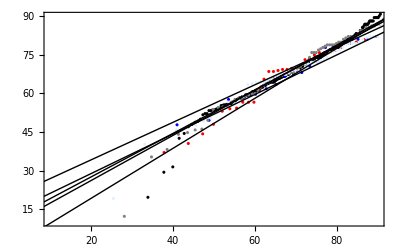

```mathematica
QuantilePlot[{fnorm,fcd,fhyp,fsttc,fmi},PlotRange->{{10,90},{10,90}},PlotStyle->{Black,Red,Blue,Gray,LightBlue}]
```

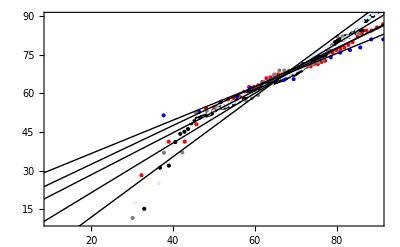

```mathematica
QuantilePlot[{mnorm,mcd,mhyp,msttc,mmi},PlotRange->{{10,90},{10,90}},PlotStyle->{Black,Red,Blue,Gray,LightBlue}]
```

Definitely deviating at the ends, indicating skew. But lets power through anyway.

#### ANOVA

```mathematica
ANOVA[data[[2;;,All]],{sex,disease,All},{sex,disease},PostTests->Bonferroni]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
sex | 1 | 1949.63 | 1949.63 | 7.72473 | 0.00555042
disease | 4 | 3527.84 | 881.959 | 3.49446 | 0.0076417
disease sex | 4 | 1236.55 | 309.137 | 1.22485 | 0.298535
Error | 987 | 249106. | 252.388 |  | 
Total | 996 | 255821. |  |  | ,CellMeans→All | 71.6207
sex[F] | 72.8814
sex[M] | 70.0696
disease[CD] | 70.797
disease[HYP] | 75.7764
disease[MI] | 73.5895
disease[NORM] | 70.2638
disease[STTC] | 74.3893
disease[CD] sex[F] | 68.4088
disease[CD] sex[M] | 72.3585
disease[HYP] sex[F] | 76.3167
disease[HYP] sex[M] | 75.187
disease[MI] sex[F] | 76.1221
disease[MI] sex[M] | 71.3967
disease[NORM] sex[F] | 71.8274
disease[NORM] sex[M] | 68.1707
disease[STTC] sex[F] | 75.0101
disease[STTC] sex[M] | 73.1043,PostTests→{sex→Bonferroni | {F,M},disease→Bonferroni | {}}}

CellMeans lists the means of each group, each combination of groups, and the overall mean.
There are 2-1=1 degrees of freedom for sex,  5-1=4 for diseases, and (2-1)*(5-1)=4 for the interaction.
Within individual groups there are  996 degrees of freedom.
The first three columns of the rows labelled sex and disease display the between-group statistics for those groups (same as for the one-way ANOVA).
The first three columns of the row labelled disease sex displays the between-group statistics for groups where sex and disease are separated
The row labelled Error displays the within-group statistics for all groups combined.
The fourth column FRatio displays the ratio of variances Model:Error for the three cases
The fifth column PValue displays the p-value associated with these FRatio values, assuming FRatio is distributed according to an F-distribution.

Conclusions

There was a significant effect of gender (p = 0.0055 < 0.05) on heart rate.
There was a significant effect of disease (p = 0.0076 < 0.05) on heart rate. 
There was no significant effect for disease and gender (p = 0.298 > 0.05) on heart rate.
The data suggests that women have higher heart rate on an average than men, and that certain diseases show significantly different heart rate from the average.